```mathematica
ClearAll[sideEffect]
ClearAll[print]
sideEffect[f_][x_]:=(f@x;x)
print[f_][x_]:=sideEffect[Print@*f@x][x]
```

```mathematica
styleLarge[x_]:=Style[x,Large]
SetAttributes[styleLarge,Listable]
```

```mathematica
FileNameJoin@{NotebookDirectory[],"figures","dasd"<>"."<>"pdf"}
```

C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\figures\dasd.pdf

```mathematica
CreateDirectory[FileNameJoin@{NotebookDirectory[],"figures"}];save[name_String,thing_,format_String:"pdf",dpi_Integer:500]:=Export[FileNameJoin@{NotebookDirectory[],"figures",name<>"."<>format},thing,ImageResolution->dpi]
```

CreateDirectory::eexist: C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\figures already exists.

### Lab Calculations

```mathematica
Subscript[a, Si]=5.4309; (*Si*)
Subscript[a, Ni]=3.5239; (*Ni*)
Subscript[a, Cu]=3.6148; (*Cu*)
(*a=Subscript[a, Si]*)
λ=1.5418;
```

```mathematica
ClearAll@d
Subscript[d, hkl_,a_:Subscript[a, Si]]:=a/(√(Total@(IntegerDigits[hkl]^2)))
```

```mathematica
Table[
{n,hkl,
#(θ/.Solve[n λ==2 Subscript[d, hkl,Subscript[a, Cu]] Sin[θ °],θ])&/@{1,2}
},
{n,1,1},
{hkl,{111,200,220,311,222,400,331,420,422}}
]ᵀ//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

1 | 
111 | 
21.6774 | 43.3549
1 | 
200 | 
25.2472 | 50.4944
1 | 
220 | 
37.0992 | 74.1983
1 | 
311 | 
45.0165 | 90.033
1 | 
222 | 
47.626 | 95.2521
1 | 
400 | 
58.5448 | 117.09
1 | 
331 | 
68.3707 | 136.741
1 | 
420 | 
72.5039 | 145.008
1 | 
422 | 
90.-17.0808 ⅈ | 180.-34.1617 ⅈ

```mathematica
VernierFormat2`VernierFormat2Import[filename_String,options___]:=Module[
{stream,head,data},
stream=OpenRead[filename];
head=ReadList[stream,"String",7];
data=Partition[ReadList[stream,"Number"],2];
Close[stream];
{
"Header"->head,
"Data"->data
}
]
```

```mathematica
ImportExport`RegisterImport[
"VernierFormat2",
VernierFormat2`VernierFormat2Import
]
```

```mathematica
hklLookupTable={{100, 110, 111, 200, 210, 211, {}, 220, {300,221}, 310, 311, 222, 320, 321, {}, 400, {410,322}, {411,330}, 331, 420, 421, 332, {}, 422, {500,430}}}[[1]]//print@Length;
```

25

## Analysis

```mathematica
axesLabel={"Angle (°)","Voltage (V)"};
```

```mathematica
dataFiles=FileNames["*.txt",NotebookDirectory[]<>"XRayLab"];
TableForm@dataFiles
data=Table[{StringSplit[FileNameSplit[path][[-1]],"."][[1]],Import[path,{"VernierFormat2","Data"}]},{path,dataFiles}];
```

C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1979_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1984_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi158_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi54_40_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni18Cu82_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni47Cu53_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni74Cu26_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi100_70.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi130_120.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi160_140.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi55_42.125_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi60_40.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Silicon80_20.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Unknown50min_160_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\UnknownLast30Min_63_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\USNickel_50_43_Fine.txt

```mathematica
names={"1979 Canadian Nickel","1984 Canadian Nickel","CuSi","CuSi","Ni_18Cu_82","Ni_47Cu_53","Ni_74Cu_26","NiSi","NiSi","NiSi","NiSi","NiSi","Silicon","Unknown Sample","Unknown Sample","US Nickel"};
namesMap=Association@Table[data[[i,1]]->names[[i]],{i,1,Length@data}];
nameToIndex[name_String]:=Module[
{position},
position=Position[data[[;;,1]],name];
If[
position=={},
Position[names,name],
position
][[1,1]]
]
```

```mathematica
Flatten[Table[{data[[idx,1]],data[[idx,2,Table[Position[data[[idx,2]],peak][[1,1]],{peak,savedPeaks[[idx]]}]]]},{idx,{nameToIndex@"Ni_18Cu_82",nameToIndex@"Ni_47Cu_53",nameToIndex@"Ni_74Cu_26"}}]ᵀ,1]
```

{Ni18Cu82_48_43_Fine,Ni47Cu53_48_43_Fine,Ni74Cu26_50_43_Fine,{{23.925,1.0775},{22.0625,3.45875}},{{23.9,1.0275},{22.35,3.45375}},{{24.1625,1.86},{22.4,0.44375}}}

```mathematica
data[[,1]]
```

{Ni18Cu82_48_43_Fine,Ni47Cu53_48_43_Fine,Ni74Cu26_50_43_Fine}

```mathematica
fullSpeed=Table[!StringContainsQ[file,"Fine"],{file,dataFiles}];
slope=1/2+3/2 Boole@fullSpeed
measurementAngles=Table[
ToExpression/@StringTrim[Take[StringSplit[StringSplit[FileNameSplit[file][[-1]],".txt"][[1]],"_"]/."Fine"|"det"->Nothing,-2],Except@DigitCharacter..],
{file,dataFiles}
]
minToAngle[i_][min_]:=measurementAngles[[i,1]]-slope[[i]]min
angles=Table[minToAngle[i]/@data[[i,2,;;,1]],{i,Length@data}];
data=Table[{data[[i,1]],{angles[[i]]/2,data[[i,2,;;,2]]}ᵀ},{i,Length@data}];
uncertainties=Table[1/2 Ceiling[1/40 it[[3]]]/(it[[3]]/((Subtract@@it[[1]])/it[[2]]))it[[2]]//N,{it,{measurementAngles,slope,Length/@data[[;;,2]]}ᵀ}]
TableForm[
Table[
{it[[4]],(Subtract@@it[[1]])/it[[2]]//N,it[[3]]/((Subtract@@it[[1]])/it[[2]])//N,Ceiling[1/40 it[[3]]],it[[5]]},
{it,{measurementAngles,slope,Length/@data[[;;,2]],data[[;;,1]],uncertainties}ᵀ}
],
TableHeadings->{None,{"Run","Minutes","Samples/Min","Window Size","Peak Uncertainty (°)"}}
]//sideEffect[save["runData",#]&]
```

{1/2,1/2,2,1/2,1/2,1/2,1/2,2,2,2,1/2,2,2,2,2,1/2}

{{50,43},{50,43},{158,0},{54,40},{48,43},{48,43},{50,43},{100,70},{130,120},{160,140},{55,42.125},{60,40},{80,20},{160,0},{63,0},{50,43}}

{0.0875,0.0875,2.,0.175,0.0625,0.0625,0.0875,0.4,0.133333,0.266667,0.1625,0.266667,0.8,2.,0.8,0.0875}

Run | Minutes | Samples/Min | Window Size | Peak Uncertainty (°)
CANickel1979_50_43_Fine | 14. | 20. | 7 | 0.0875
CANickel1984_50_43_Fine | 14. | 20. | 7 | 0.0875
CuSi158_0 | 79. | 20. | 40 | 2.
CuSi54_40_Fine | 28. | 20. | 14 | 0.175
Ni18Cu82_48_43_Fine | 10. | 20. | 5 | 0.0625
Ni47Cu53_48_43_Fine | 10. | 20. | 5 | 0.0625
Ni74Cu26_50_43_Fine | 14. | 20. | 7 | 0.0875
NiSi100_70 | 15. | 30. | 12 | 0.4
NiSi130_120 | 5. | 30. | 4 | 0.133333
NiSi160_140 | 10. | 30. | 8 | 0.266667
NiSi55_42 | 25.75 | 20. | 13 | 0.1625
NiSi60_40 | 10. | 30. | 8 | 0.266667
Silicon80_20 | 30. | 10. | 8 | 0.8
Unknown50min_160_0 | 80. | 20. | 40 | 2.
UnknownLast30Min_63_0 | 31.5 | 20. | 16 | 0.8
USNickel_50_43_Fine | 14. | 20. | 7 | 0.0875

0.025

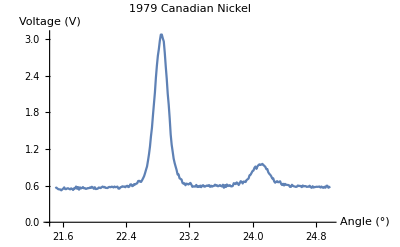
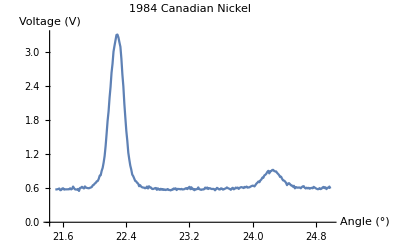
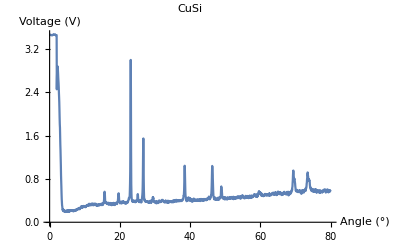
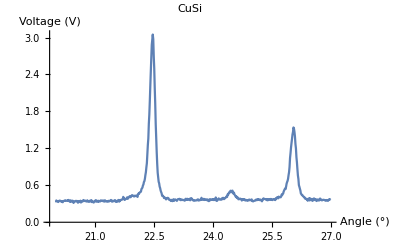
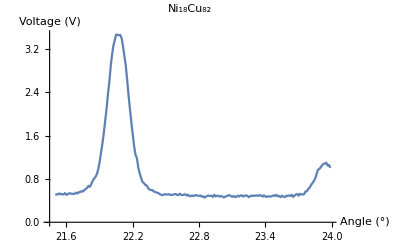
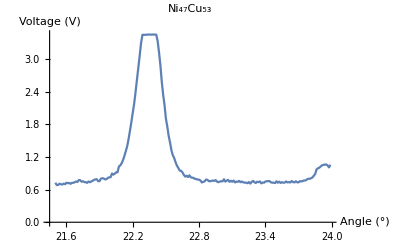
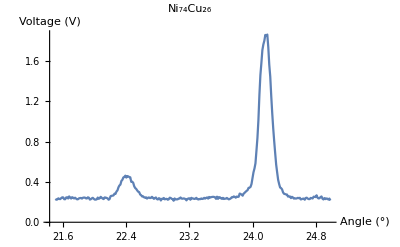
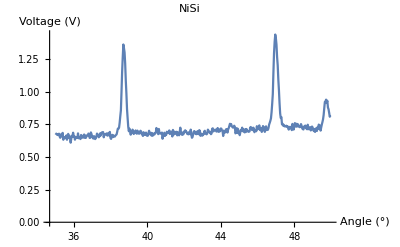

```mathematica
Table[ListPlot[datum[[2]],PlotLabel->namesMap[[datum[[1]]]],Joined->True,PlotRange->Full,AxesLabel->axesLabel],{datum,data}]
```

#### Peak finding for each run

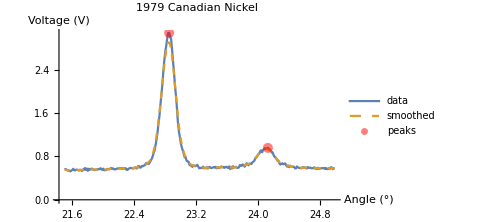
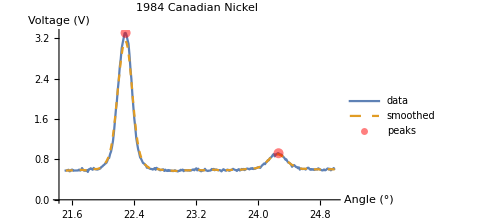
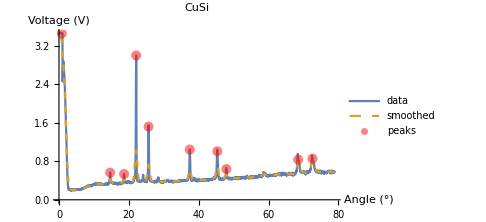
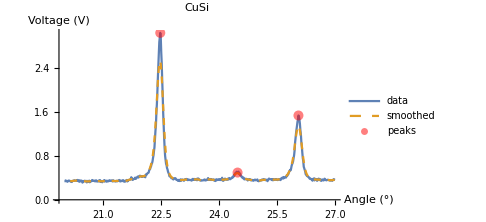
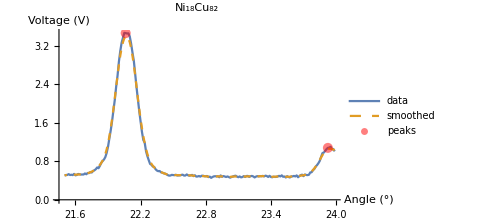
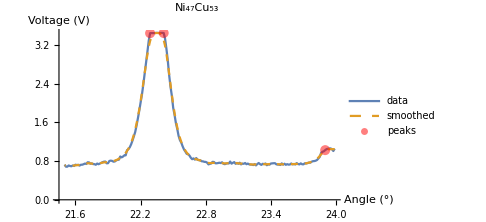
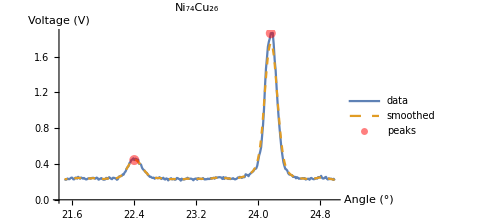
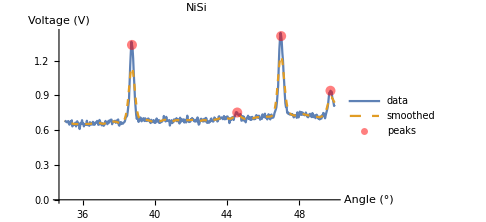
-Graphics- | 24.125
22.85
-Graphics- | 24.2625
22.2875
-Graphics- | 72.6
68.5
47.95
45.35
37.45
25.65
22.1
18.65
14.65
0.799995
-Graphics- | 26.05
24.475
22.475
-Graphics- | 23.925
22.0625
-Graphics- | 23.9
22.4125
22.2875
-Graphics- | 24.1625
22.4
-Graphics- | 49.7333
47.
44.5667
38.7333
-Graphics- | 64.9667
64.5667
64.2
63.7333
63.0667
62.4333
61.7333
61.4667
61.1
60.4333
60.0667
-Graphics- | 79.
78.3333
73.3333
72.8333
-Graphics- | 26.4875
24.2375
22.8
-Graphics- | 26.0333
23.7667
22.3333
-Graphics- | 38.2
34.5
28.
23.5
14.1
-Graphics- | 78.85
66.9
51.25
44.35
37.35
30.8
-Graphics- | 29.45
20.35
1.75
-Graphics- | 24.05
22.2125

```mathematica
Table[Module[
{title,runAngles,runVoltages,filterRadius,σ,runVoltagesSmooth,runDataSmooth,n,ker,convolved,s,peakIdx,peakV,peakAngle,peaks,plot},
{title,runData}=runData;
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles];
σ=√filterRadius;
(*σ=filterRadius/2;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=ArrayPad[{-2n},n,1];
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Fixed"]];
(*convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];*)
(*s=0.0006;*)
s=StandardDeviation@convolved/3.1;
(*s=StandardDeviation@convolved/5;*)
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ;
peakAngle=runAngles[[peakIdx]];
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
plot=ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"data","smoothed","peaks"},
PlotLabel->namesMap@title,
AxesLabel->axesLabel,
ImageSize->Medium
];
(*save[title<>"_with_smooth",plot];*)
{plot,peakAngle}
],
{runData,data}
]//TableForm
```

```mathematica
FullForm@{{24.1249999405}, {22.84999990475}}
```

List[List[24.125],List[22.85]]

```mathematica
savedPeaks=Flatten[Flatten[{{{{24.1249999405}, {22.84999990475}}}, {{{24.262499988}, {22.28749990475}}}, {{{72.599999428}, {68.499999046}, {58.799999237}, {47.949998856}, {45.349998474}, {37.449996948}, {25.649997710999997}, {22.099998474000003}, {18.649997710999997}, {14.649993895999998}, {0.799995421999995}}}, {{{26.04999995225}, {24.47499990475}, {22.47499990475}}}, {{{23.924999997}, {22.06249988075}}}, {{{23.899999991}, {22.41249990475}, {22.28749990475}}}, {{{24.16249996425}, {22.399999857}}}, {{{49.733333319}, {46.999999762}, {44.566666603}, {38.733332634}}}, {{{64.966666665}, {64.566666633}, {64.199999928}, {63.73333323}, {63.066666603}, {62.433333157999996}, {61.733333111}, {61.46666646}, {61.099999905}, {60.43333292}, {60.066666603}}}, {{{79.}, {78.333333254}, {73.333333015}, {72.833333015}}}, {{{26.48749995225}, {24.237499714000002}, {22.799999714000002}}}, {{{26.033332109}, {23.766664982}, {22.333331108}}}, {{{38.199999928}, {34.499999523}, {27.999999046}, {23.5}, {14.099998474}}}, {{{78.849999905}, {66.899999619}, {51.249998093}, {44.349998474}, {37.349998474}}}, {{{29.449999809}, {20.349999428}, {1.7499980929999985}}}, {{{24.04999995225}, {22.212499857}}}},{{1},{4}}],2];
Length@savedPeaks==Length@data
Dimensions/@savedPeaks
```

True

{{2},{2},{11},{3},{2},{3},{2},{4},{11},{4},{3},{3},{5},{5},{3},{2}}

#### Some of them need to be fixed by hand, so those are here:

```mathematica
savedPeaks=Flatten[Flatten[{{{{24.1249999405}, {22.84999990475}}}, {{{24.262499988}, {22.28749990475}}}, {{{72.599999428}, {68.499999046}, {58.799999237}, {47.949998856}, {45.349998474}, {37.449996948}, {28.449996948}, {25.649997710999997}, {24.099998474000003}, {22.099998474000003}, {18.649997710999997}, {14.649993895999998}}}, {{{26.04999995225}, {24.47499990475}, {22.47499990475}}}, {{{23.924999997}, {22.06249988075}}}, {{{23.899999991}, {(22.41249990475+22.28749990475)/2}}}, {{{24.16249996425}, {22.399999857}}}, {{{49.733333319}, {46.999999762}, {44.566666603}, {38.733332634}}}, {{{64.966666665}, {64.566666633}, {64.199999928}, {63.73333323}, {63.066666603}, {62.433333157999996}, {61.733333111}, {61.46666646}, {61.099999905}, {60.43333292}, {60.066666603}}}, {{{79.}, {78.333333254}, {73.333333015}, {72.833333015}}}, {{{26.48749995225}, {24.237499714000002}, {22.799999714000002}}}, {{{26.033332109}, {23.766664982}, {22.333331108}}}, {{{38.199999928}, {34.499999523}, {27.999999046}, {23.5}, {14.099998474}}}, {{{78.849999905}, {66.899999619}, {51.249998093}, {44.349998474}, {37.349998474}}}, {{{29.449999809}, {20.349999428}, {1.7499980929999985}}}, {{{24.04999995225}, {22.212499857}}}},{{1},{4}}],2];
Length@savedPeaks==Length@data
Dimensions/@savedPeaks
```

True

{{2},{2},{12},{3},{2},{2},{2},{4},{11},{4},{3},{3},{5},{5},{3},{2}}

```mathematica
elSymb=Ni;
{elName,name}=<|Cu->{"Copper","CuSi54_40_Fine"},Ni->{"Nickel","NiSi60_40"}|>[elSymb];
idx=nameToIndex@name;
runData=data[[idx,2]];
Length@runData
(*measured=Insert[
Reverse[runData[[Flatten[Table[Position[runData[[;;,1]],peak],{peak,savedPeaks[[idx]]}]]]]],
{"uh","no"},
8
]*)
(*
CuSi158_0
{{111,Si},{110,Cu},{111,Cu},{220,Si},{200,Cu},{311,Si},{220,Cu},{311,Cu},{222,Cu},{400,Cu},{331,Cu},{420,Cu}}
/.{Cu,110,17.553621061460667,18.649997710999997,0.534999967}->{"??","???","???????",18.649997710999997,0.534999967}
*)
measured=Reverse[runData[[Flatten[Table[Position[runData[[;;,1]],peak],{peak,savedPeaks[[idx]]}]]]]]
TableForm[
Join[
Table[
{
hkla[[2]],
hkla[[1]],
(θ/.Solve[ λ==2 Subscript[d, hkla[[1]],Subscript[a, hkla[[2]]]] Sin[θ °],θ])[[1]]
},
{hkla,{{111,elSymb},{220,Si},{200,elSymb}}}
]ᵀ,
measuredᵀ
]ᵀ,
TableHeadings->{None, {"Source","hkl","Theoretical θ (°)","Measured θ (°)","Measured Voltage (V)"}}
]//sideEffect[save["Measured"<>elName<>"SpectrumZoomed",#]&]
```

300

{{22.3333,2.595},{23.7667,0.785},{26.0333,1.65}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Source | hkl | Theoretical θ (°) | Measured θ (°) | Measured Voltage (V)
Ni | 111 | 22.2661 | 22.3333 | 2.595
Si | 220 | 23.6712 | 23.7667 | 0.785
Ni | 200 | 25.9462 | 26.0333 | 1.65

```mathematica
peakSi220Theory=(θ/.Solve[ λ==2 Subscript[d, 220,Subscript[a, Si]] Sin[θ °],θ])[[1]]
peakSi220Meas=measured[[2,1]];
delta=peakSi220Meas-peakSi220Theory;
{measuredAngles,measuredVoltages}=(measured[[{1,3},;;]]-Table[{delta,0},2])ᵀ;
measuredAngles=Around[measuredAngles,uncertainties[[idx]]]
{hkls,theory}=Table[
{
hkla[[1]],
(θ/.Solve[ λ==2 Subscript[d, hkla[[1]],Subscript[a, hkla[[2]]]] Sin[θ °],θ])[[1]]
},
{hkla,{{111,elSymb},{200,elSymb}}}
]ᵀ;
TableForm[
Join@{hkls,
theory,
measuredAngles,
(measuredAngles-theory)/theory 100,
measuredVoltages
}ᵀ,
TableHeadings->{None, {"hkl","Theoretical θ (°)","Measured θ (°)","Error (%)","Measured Voltage (V)"}}
]//sideEffect[save["Measured"<>elName<>"SpectrumZoomedAdjusted",#]&]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

23.6712

{22.240.27,25.940.27}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

hkl | Theoretical θ (°) | Measured θ (°) | Error (%) | Measured Voltage (V)
111 | 22.2661 | 22.240.27 | -0.11.2 | 2.595
200 | 25.9462 | 25.940.27 | 0.01.0 | 1.65

```mathematica
measuredAngles
Sin@%
```

{22.240.27,25.940.27}

{-0.240.26,0.720.18}

```mathematica
Subscript[a, Ni]
Subscript[a, Cu]
```

3.5239

3.6148

```mathematica
Subscript[aMeas, elSymb]=Table[
a/.Solve[λ==2 a/(√(Total@(IntegerDigits[hkls[[i]]]^2)))Sin[measuredAngles[[i]] °],a][[1,1]],
{i,Length@hkls}
]//Mean
```

3.5270.026

```mathematica
Subscript[aMeas, Cu]
```

3.6150.018

```mathematica
Dimensions[Flatten[
Table[
{data[[idx,2]],data[[idx,2,Table[Position[data[[idx,2]],peak][[1,1]],{peak,savedPeaks[[idx]]}]]]},
{idx,{nameToIndex@"Ni_18Cu_82",nameToIndex@"Ni_47Cu_53",nameToIndex@"Ni_74Cu_26"}}
]ᵀ,
1
][[4]]]
```

{2,2}

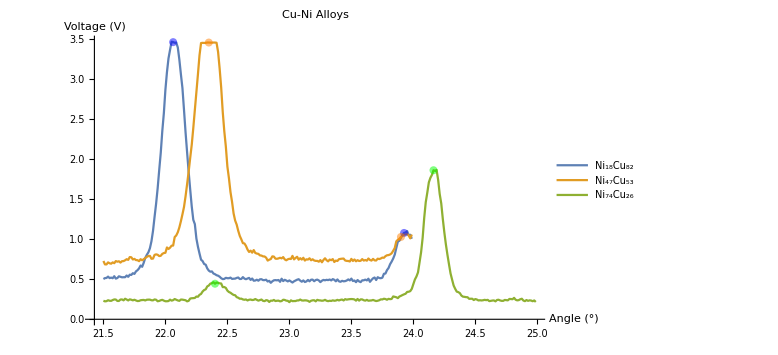

```mathematica
ListPlot[
Flatten[
Table[
{data[[idx,2]],data[[idx,2,Table[Position[data[[idx,2]],peak][[1,1]],{peak,savedPeaks[[idx]]}]]]},
{idx,{nameToIndex@"Ni_18Cu_82",nameToIndex@"Ni_47Cu_53",nameToIndex@"Ni_74Cu_26"}}
]ᵀ,
1
],
Joined->{True,True,True,False,False,False},
PlotRange->Full,
PlotStyle->{Automatic,Automatic,Automatic,Directive[Blue,PointSize[.01],Opacity[0.5]],Directive[Orange,PointSize[.01],Opacity[0.5]],Directive[Green,PointSize[.01],Opacity[0.5]]},
AxesLabel->axesLabel,
ImageSize->Large,
PlotLabel->"Cu-Ni Alloys",
PlotLegends->{"Ni_18Cu_82","Ni_47Cu_53","Ni_74Cu_26"}
]//sideEffect[save["alloys",#]&]
```

```mathematica
idx=5 (*5,6,7*)
runData=data[[idx,2]];
Length@runData
measured=Reverse[runData[[Flatten[Table[Position[runData[[;;,1]],peak],{peak,savedPeaks[[idx]]}]]]]]
TableForm[
Join[
Table[
{
hkla[[2]],
hkla[[1]],
(θ/.Solve[ λ==2 Subscript[d, hkla[[1]],Subscript[a, hkla[[2]]]] Sin[θ °],θ])[[1]]
},
{hkla,{{111,elSymb},{220,Si}}}
]ᵀ,
measuredᵀ
]ᵀ,
TableHeadings->{None, {"Source","hkl","Theoretical θ (°)","Measured θ (°)","Measured Voltage (V)"}}
]
(*//sideEffect[save["Measured"<>elName<>"SpectrumZoomed",#]&]*)
```

5

200

{{22.0625,3.45875},{23.925,1.0775}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Source | hkl | Theoretical θ (°) | Measured θ (°) | Measured Voltage (V)
Ni | 111 | 22.2661 | 22.0625 | 3.45875
Si | 220 | 23.6712 | 23.925 | 1.0775

```mathematica
peakSi220Theory=(θ/.Solve[ λ==2 Subscript[d, 220,Subscript[a, Si]] Sin[θ °],θ])[[1]]
peakSi220Meas=measured[[2,1]]
delta=peakSi220Meas-peakSi220Theory
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

23.6712

23.925

0.253844

```mathematica
deltas={0.25384372377229525,0.22884371777229617,0.49134369102229414}
```

{0.253844,0.228844,0.491344}

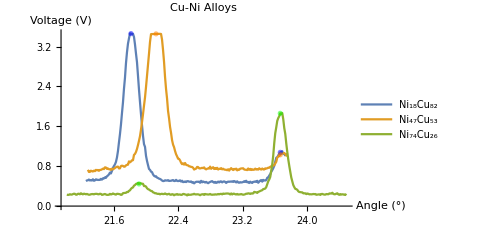

```mathematica
ListPlot[
Flatten[
Table[
(
{angles,voltages}=data[[idx,2]]ᵀ;
delta=deltas[[idx-4]];
angles=angles-delta;
datum={angles,voltages}ᵀ;
{datum,datum[[Table[Position[datum,peak-delta][[1,1]],{peak,savedPeaks[[idx]]}]]]}
),
(*{idx,nameToIndex/@{"Ni_18Cu_82"}}*)
{idx,nameToIndex/@{"Ni_18Cu_82","Ni_47Cu_53","Ni_74Cu_26"}}
]ᵀ,
1
],
Joined->{True,True,True,False,False,False},
PlotRange->Full,
PlotStyle->{Automatic,Automatic,Automatic,Directive[Blue,PointSize[.01],Opacity[0.5]],Directive[Orange,PointSize[.01],Opacity[0.5]],Directive[Green,PointSize[.01],Opacity[0.5]]},
AxesLabel->axesLabel,
ImageSize->Large,
PlotLabel->"Cu-Ni Alloys",
PlotLegends->{"Ni_18Cu_82","Ni_47Cu_53","Ni_74Cu_26"}
]//sideEffect[save["alloysShifted",#]&]
```

```mathematica
fractionCu={100,82,52,26,0};
```

Cu Fraction (%) | Ni/Cu Peak (°) | a (Å)
82 | 21.810.06 | 3.5940.010
52 | 22.120.06 | 3.5460.010
26 | 21.910.09 | 3.5780.014

FittedModel[3.53167+0.000697806 x]

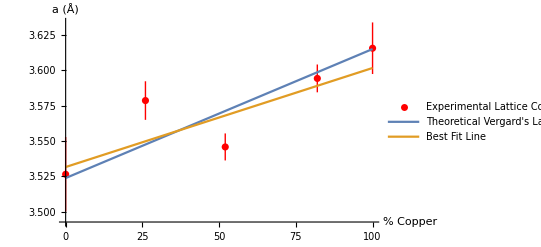

```mathematica
alloyData=Table[(
angle=Around[savedPeaks[[idx,2]],uncertainties[[idx]]]-deltas[[idx-4]];
thisa=a/.Solve[λ==2 a/(√(Total@(IntegerDigits[111]^2)))Sin[angle °],a][[1,1]];
{fractionCu[[idx-3]],angle,thisa}
),{idx,{5,6,7}}
]//print[TableForm[#,TableHeadings->{None, {"Cu Fraction (%)","Ni/Cu Peak (°)","a (Å)"}}]&];
alloyData={
fractionCu,
Join[{Subscript[aMeas, Cu]},alloyData[[;;,3]],{Subscript[aMeas, Ni]}]
}ᵀ//sideEffect[save["alloyTable",TableForm[#,TableHeadings->{None, {"Cu Fraction (%)","a (Å)"}}]]&];
{aMeasured,σ}={#["Value"],#["Uncertainty"]}&/@alloyData[[;;,2]]ᵀ;
fit=LinearModelFit[{fractionCu,aMeasured}ᵀ,x,x,Weights->1/σ^2,VarianceEstimatorFunction->(1&)]//print@Identity;
Show[
ListPlot[
alloyData,
PlotStyle->Red,
PlotRange->Full,
AxesLabel->{"% Copper","a (Å)"},
PlotLegends->styleLarge@{"Experimental Lattice Constants"}
],
Plot[
{
(x/100 Subscript[a, Cu]+(1-x/100)Subscript[a, Ni]),
Normal[fit]
},
{x,0,100},
PlotRange->Full,
PlotLegends->styleLarge@{"Theoretical Vergard's Law","Best Fit Line"}
],
ImageSize->Full,
AxesStyle->Large
]//sideEffect[save["alloyFits",#]&]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

23.6712

24.1625

0.491344

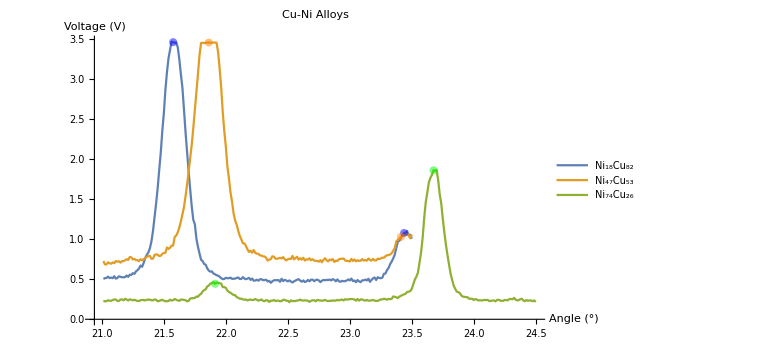

```mathematica
(*{measuredAngles,measuredVoltages}=(measured[[1]]-{delta,0})ᵀ;
measuredAngles=Around[measuredAngles,uncertainties[[idx]]]
{hkls,theory}=Table[
{
hkla[[1]],
(θ/.Solve[ λ==2 Subscript[d, hkla[[1]],Subscript[a, hkla[[2]]]] Sin[θ °],θ])[[1]]
},
{hkla,{{111,elSymb},{200,elSymb}}}
]ᵀ;
TableForm[
Join@{hkls,
theory,
measuredAngles,
(measuredAngles-theory)/theory 100,
measuredVoltages
}ᵀ,
TableHeadings->{None, {"hkl","Theoretical θ (°)","Measured θ (°)","Error (%)","Measured Voltage (V)"}}
]*)
(*//sideEffect[save["Measured"<>elName<>"SpectrumZoomedAdjusted",#]&]*)
```

```mathematica
idx=nameToIndex@name;
runData=data[[idx,2]];
Reverse[runData[[Flatten[Table[Position[runData[[;;,1]],peak],{peak,savedPeaks[[idx]]}]]]]]ᵀ
```

{}

```mathematica
TableForm[
{
Table[
{
hkl,
(θ/.Solve[λ==2 Subscript[d, hkl,Subscript[a, Si]] Sin[θ °],θ])[[1]]
},
{hkl,{111,200,220,311,222,400,331,420}}
]ᵀ
},
TableHeadings->{None, {"hkl","Theoretical θ (°)","Measured θ (°)","Measured Voltage (V)"}}
]//sideEffect[save["CopperSpectrum",#]&]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

hkl | Theoretical θ (°)
111
200
220
311
222
400
331
420 | 29.4536
34.5961
53.415
70.3169
79.5576
90.-29.508 ⅈ
90.-38.7432 ⅈ
90.-41.1812 ⅈ

```mathematica
savedPeaks[[1]]
```

{24.125,22.85}

```mathematica
savedPeaks[[nameToIndex["Silicon"]]]
```

{38.2,34.5,28.,23.5,14.1}

```mathematica
closestPosition[list_,elem_]:=Module[
{positions},
positions=Position[list,elem]
]
savedPeaks[[1]]
(*Position[data[[1,2]],%[[1]]]*)
Table[
Position[data[[1,2]],blah][[1,1]],
{blah,%}
]
data[[1,2,%]]
```

{24.125,22.85}

{70,172}

{{24.125,0.95625},{22.85,3.075}}

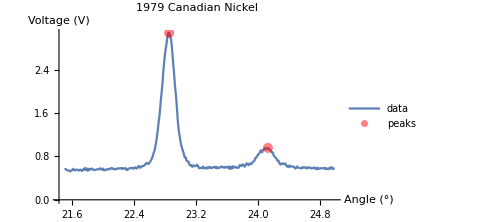
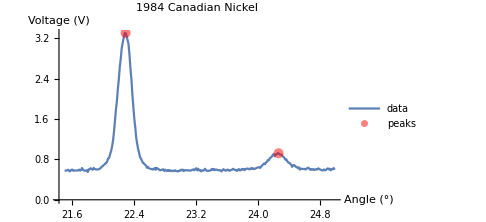
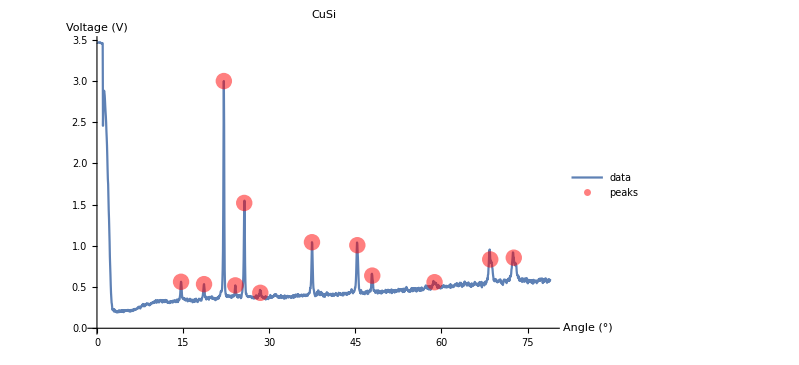
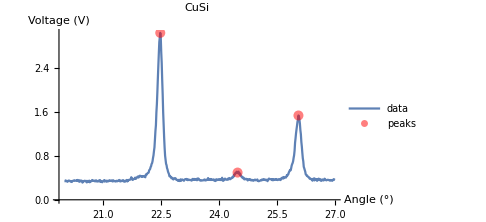
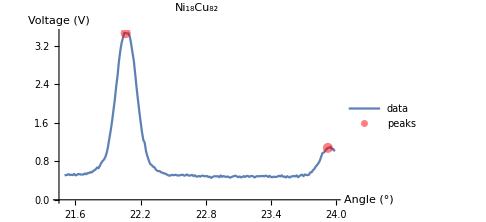
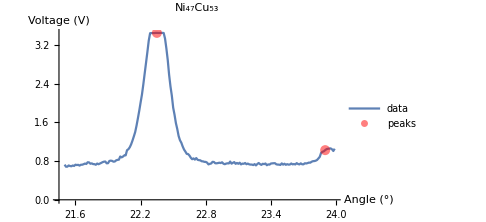
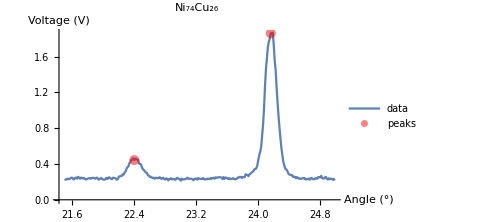
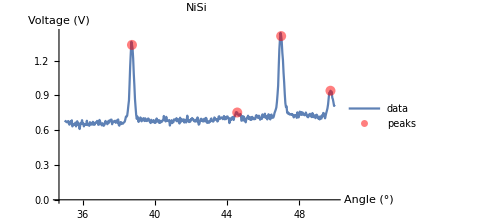

```mathematica
Table[
(
{runData,peakAngles}=datum;
{title,runData}=runData;
peaks=runData[[Table[Position[runData,peak][[1,1]],{peak,peakAngles}]]];
(*Print@peaks;*)
plot=ListPlot[
{runData,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"data","peaks"},
PlotLabel->namesMap@title,
AxesLabel->axesLabel,
ImageSize->Medium(*,
TicksStyle->Large*)
];
save[title,plot];
plot
),
{datum,{data,savedPeaks}ᵀ}
]
```

```mathematica
{data,savedPeaks}ᵀ[[nameToIndex@"CuSi"]][[2]]
```

{72.6,68.5,58.8,47.95,45.35,37.45,28.45,25.65,24.1,22.1,18.65,14.65}

```mathematica
peakLabels=Reverse@{"Si 111","?","Cu 111","Si 220","Cu 200","Si 311","Cu 220","Cu 311","Cu 222","Cu 400","Cu 331","Cu 420"}
```

{Cu 420,Cu 331,Cu 400,Cu 222,Cu 311,Cu 220,Si 311,Cu 200,Si 220,Cu 111,?,Si 111}

```mathematica
{runData,peakAngles}={data,savedPeaks}ᵀ[[nameToIndex@"CuSi"]];
{title,runData}=runData;
peaks=runData[[Table[Position[runData,peak][[1,1]],{peak,peakAngles}]]];
(*Print@peaks;*)
plot=ListPlot[
{runData,Table[Callout[it[[1]],it[[2]],Above,CalloutStyle->Opacity[0],Background->Opacity[0],LabelStyle->Medium],{it,{peaks,peakLabels}ᵀ}]},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{Style["data",Large],Style["peaks",Large]},
PlotLabel->namesMap@title,
AxesLabel->axesLabel,
AxesStyle->Large,
ImageSize->Full,
TicksStyle->Large
];
save[title,plot];
plot
```

-Graphics-

```mathematica
runData=data[[nameToIndex@"CuSi158_0",2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles]//print@Identity;
σ=filterRadius/2//print@N@*Identity;
(*σ=√filterRadius//print@N@*Identity;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
s=0.0006;
s=StandardDeviation@convolved/3
```

40

20.

0.000129365

```mathematica
getAngles[data_,index_]:=;
getAngles[data_,indices_]:=;
```

```mathematica
{peakIdx,peakV}=FindPeaks[runVoltagesSmooth]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

```mathematica
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ
peakAngle=runAngles[[peakIdx]]
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

{{57,102,116,123,131,135,140,198,203,210,222,224,280,287,462,584,594,620,635,658,669,672,678,683,710,792,823,827,832,839,841,868,1027,1066,1069,1072,1099,1105,1137,1144,1177,1275,1288,1325,1567,1573},{0.000140024,0.000136684,0.000200726,0.000403425,0.000253874,0.000233553,0.000235566,0.00033513,0.000217659,0.000345864,0.00016372,0.000141425,0.00019729,0.000189762,0.000137567,0.000190828,0.000129778,0.000178452,0.000239506,0.000174854,0.000267604,0.000264723,0.000300099,0.000286707,0.000144462,0.000247692,0.000190768,0.000233476,0.000234507,0.000224307,0.000286271,0.000266226,0.000656664,0.000327827,0.000322419,0.000298785,0.00169172,0.000648355,0.000643632,0.0005084,0.00245645,0.000174119,0.000145473,0.000129646,0.00166635,0.0017157}}

{76.15,73.9,73.2,72.85,72.45,72.25,72.,69.1,68.85,68.5,67.9,67.8,65.,64.65,55.9,49.8,49.3,48.,47.25,46.1,45.55,45.4,45.1,44.85,43.5,39.4,37.85,37.65,37.4,37.05,36.95,35.6,27.65,25.7,25.55,25.4,24.05,23.75,22.15,21.8,20.15,15.25,14.6,12.75,0.649994,0.349998}

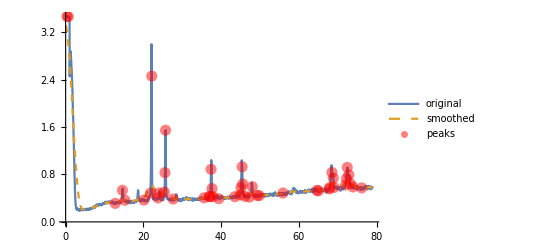

```mathematica
ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"original","smoothed","peaks"}
]
```

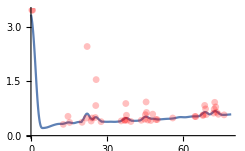

```mathematica
ListPlot[
{runDataSmooth,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.25]]},
PlotRange->Full
]
```

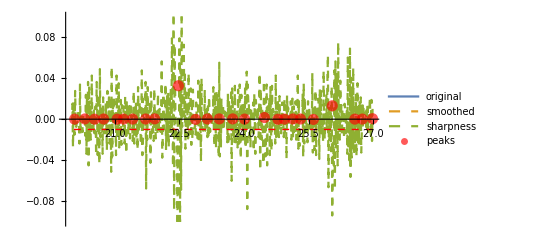

```mathematica
sharpness={runAngles,ListConvolve[{1,-2,1},ArrayPad[runVoltages,1,"Reversed"]]}ᵀ;
ListLinePlot[
{runData,runDataSmooth,sharpness,peaks},
Joined->{True,True,True,False},
PlotStyle->{Automatic,Dashed,Dashed,{Directive[Red,PointSize[.02],Opacity[0.65]]}},
PlotLegends->{"original","smoothed","sharpness","peaks"},
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-0.01},{runAngles[[-1]],-0.01}}]},
PlotRange->{-.1,.1}
]
```

0.00248099

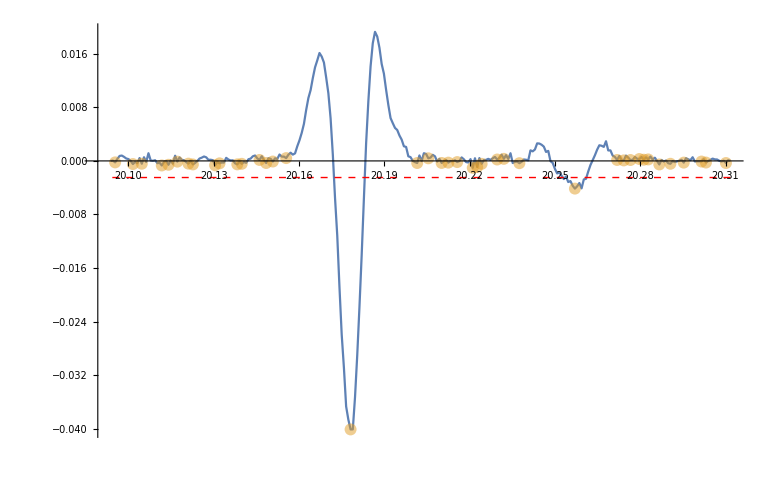

```mathematica
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3//N
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

20

4.47214

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-40,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

1.0425

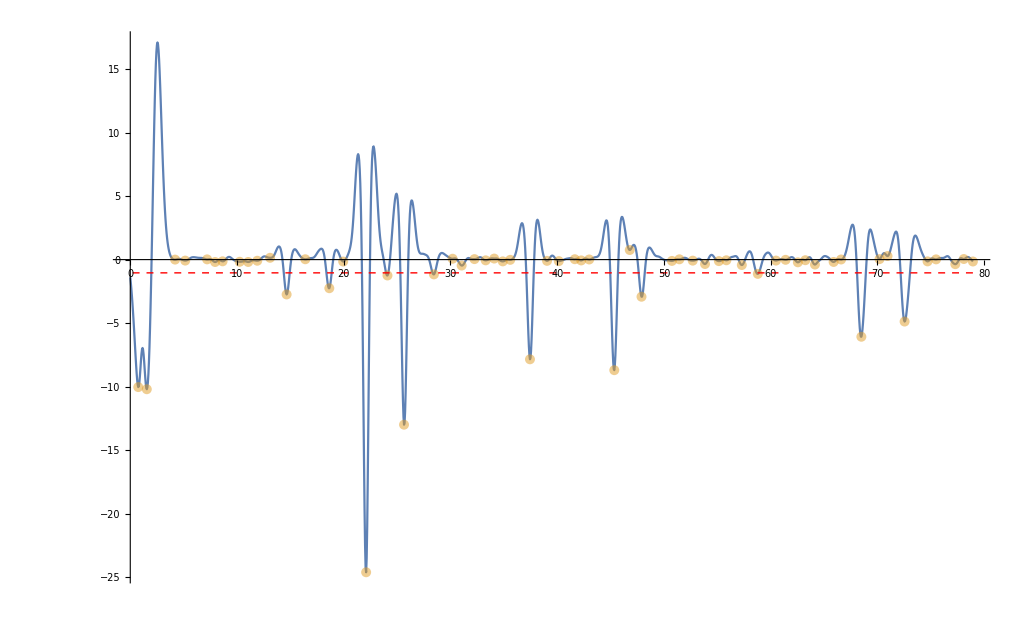

```mathematica
runData=data[[nameToIndex@"CuSi158_0",2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/80 Length@runAngles]//print@Identity;
(*σ=filterRadius/2//print@N;*)
σ=√filterRadius//print@N;
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=ArrayPad[{-2n},n,1]
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Fixed"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3.1
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5},
ImageSize->Large
]
```

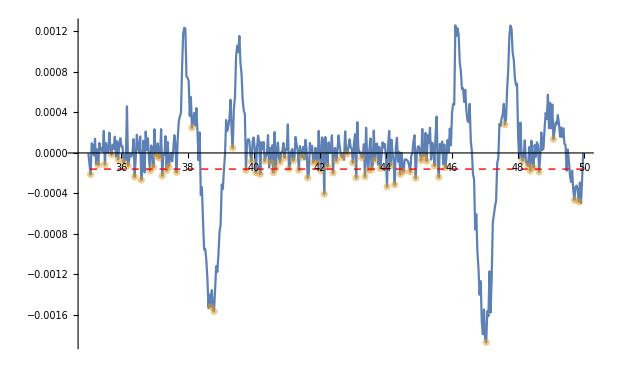

```mathematica
Table[
Module[
{},
runData=data[[6,2]];
{runAngles,runVoltages}=runDataᵀ;
σ=6;
filterRadius=Ceiling@*Sqrt@*Length@runAngles;
runVoltagesSmooth=GaussianFilter[runVoltages,filterRadius];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation@convolved/3;
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
],
{i,1,1}
]
```

```mathematica
data1[[2]]
```

{26.975,0.37375}

```mathematica
GaussianFilter[data1[[2]],{3,1.5}]
```

{17.5865,9.76229}